```mathematica
ClearAll["Global`*"]
```

## -Graphics- -Graphics-

# Separatrix plot - ABC points included

```mathematica
PacletInstall["CodeParser"]
PacletInstall["CodeInspector"];
Needs["CodeInspector`"]
```

PacletObject[…]

Export function with proper path and naming

```mathematica
export[object_,name_]:=Export[StringTemplate["/Users/basavyr/Offline-Work/Repos/phdthesis/Chapters/Figures/``.pdf"][name],object,ImageResolution->1500];
```

Separatrix equations

```mathematica
f1[u_]:=1;
fbonus2[u_]:=2;
fbonus3[u_]:=-1;
f2[u_]:=0;
f3[u_,v_]:=Sqrt[v];
f4[u_,v_]:=v;
f5[u_,v_]:=-v;
```

Critical points (u,v)

```mathematica
axis1mois={80,10,50};
axis2mois={10,40,20};
axis3mois={10,20,40};
thetaConst=70*π/180;
jConst=11/2;
Aaxis1=N[(1/(2*#))]&/@axis1mois;
Aaxis2=N[(1/(2*#))]&/@axis2mois;
Aaxis3=N[(1/(2*#))]&/@axis3mois;
j1=jConst*Cos[thetaConst];
j2=jConst*Sin[thetaConst];
Aterm[I_,A_]:=A[[2]](1-j2/I)-A[[1]];
uterm[I_,A_]:=(A[[3]]-A[[1]])/Aterm[I,A];
v0term[I_,A_]:=-(A[[1]]*j1)/Aterm[I,A];
```

```mathematica
p1axis[I_]:={uterm[I,Aaxis1],Abs[v0term[I,Aaxis1]]};
p2axis[I_]:={uterm[I,Aaxis2],Abs[v0term[I,Aaxis2]]};
p3axis[I_]:={uterm[I,Aaxis3],Abs[v0term[I,Aaxis3]]};
spin=19/2;
p1axis[spin]
p2axis[spin]
p3axis[spin]
```

{0.226608,0.710459}

{0.564329,2.12313}

{0.971482,2.43662}

Plot tools

```mathematica
inseter[text_,pos_,color_]:=Inset[Style[StringTemplate["``"][text],color,Bold,18,FontFamily->"Latin Modern Roman"],Scaled[{pos[[1]],pos[[2]]}]];
```

Phase diagram

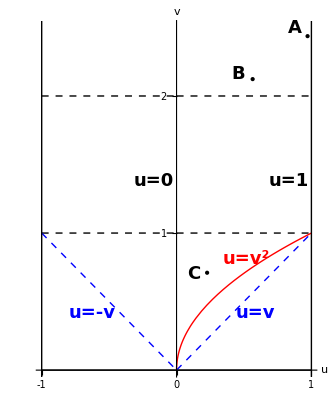

```mathematica
phaseDiagram=Plot[{f1[u],f2[u],f3[u,u],f4[u,u],f5[u,u],fbonus2[u]},{u,-1,1},
PlotRange->{0,2.5},
AspectRatio->Automatic,
Frame->False,Axes->True,
ImageSize->330,
Ticks->{{-1,0,1},{1,2}},
LabelStyle->{18,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->{{Black,Dashed,Thick},{Black,Thick},{Red,Thick},{Blue,Thick,Dashed},{Blue,Thick,Dashed},{Black,Dashed,Thick}},
AxesStyle->Directive[Thick,Black],
AxesLabel->{"u","v"},
Epilog->{inseter["u=-v",{0.2,0.18},Blue],inseter["u=v",{0.78,0.18},Blue],inseter["u=v^2",{0.75,0.33},Red],inseter["u=0",{0.42,0.55},Black],inseter["u=1",{0.9,0.55},Black],
inseter["A",{0.92,0.98},Black],inseter["B",{0.72,0.85},Black],inseter["C",{0.56,0.29},Black]}
];
Show[
phaseDiagram,
Graphics[{Thick,Black,Line[{{1,-2},{1,3}}]}],
Graphics[{Thick,Black,Line[{{-1,-2},{-1,3}}]}],
Graphics[{PointSize[Large],Black,Point[{p1axis[spin]}]}],
Graphics[{PointSize[Large],Black,Point[{p2axis[spin]}]}],
Graphics[{PointSize[Large],Black,Point[{p3axis[spin]}]}]
]
export[Show[phaseDiagram,Graphics[{Thick,Black,Line[{{1,0},{1,1}}]}],Graphics[{Thick,Black,Line[{{-1,0},{-1,1}}]}]],"new-boson-separatrix-diagram"];
```